```mathematica
uval=DSolveValue[{D[u[x,y],{x,2}]+D[u[x,y],{y,2}]==0,u[x,0]==0,u[x,2]==10,u[0,y]==0,u[4,y]==0},u,{x,0,4},{y,0,2}]
DSolveValue[{D[u[x,y],{x,2}]+D[u[x,y],{y,2}]==0,u[x,0]==10,u[x,2]==0,u[0,y]==0,u[4,y]==0},u,{x,0,4},{y,0,2}]
uvalRev=NDSolveValue[{D[u[x,y],{x,2}]+D[u[x,y],{y,2}]==0,u[x,0]==10,u[x,2]==0,u[0,y]==0,u[4,y]==0},u,{x,0,4},{y,0,2}]
```

Function[{x,y},-(20 (-1+(-1)^K[1]) Csch[1/2 π K[1]] Sin[1/4 π x K[1]] Sinh[1/4 π y K[1]])/(π K[1])K[1]1∞]

Function[{x,y},-(20 (-1+(-1)^K[1]) Csch[1/2 π K[1]] Sin[1/4 π x K[1]] Sinh[1/4 π (2-y) K[1]])/(π K[1])K[1]1∞]

InterpolatingFunction[…]

InterpolatingFunction[…]

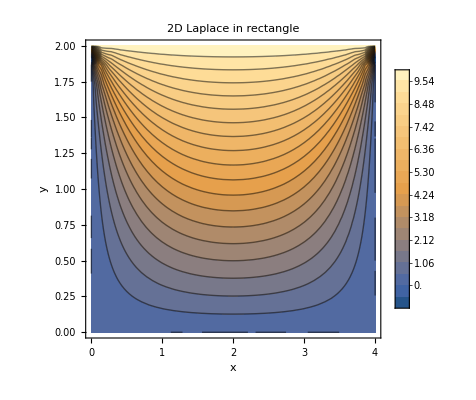

```mathematica
uval=NDSolveValue[{D[u[x,y],{x,2}]+D[u[x,y],{y,2}]==0,u[x,0]==0,u[x,2]==10,u[0,y]==0,u[4,y]==0},u,{x,0,4},{y,0,2}]

ContourPlot[uval[x,y],{x,0,4},{y,0,2},FrameLabel->{"x","y"},PlotLabel->"2D Laplace in rectangle",PlotLegends->Automatic, Contours->20]
```

```mathematica
usol[x_,y_,n_]:= Sum[(20 (1-(-1)^i)  (ⅇ^((-π i)/4 y)-ⅇ^((π i)/4 y))Sin[1/4 π x i])/((ⅇ^((-π i)/2)-ⅇ^((π i)/2))π i),{i, 1, n}]//N
usolRev[x_,y_,n_]:= Sum[(20 (1-(-1)^i)  (ⅇ^((-π i)/4(2-y))-ⅇ^((π i)/4(2-y)))Sin[1/4 π x i])/((ⅇ^((-π i)/2)-ⅇ^((π i)/2))π i),{i, 1, n}]//N
```

```mathematica
uvalRev[1,0]//N
usolRev[1,0,350] //N
```

10.

10.0001

# Сравнение с точным решением

## Сетка 0.01

```mathematica
X = Import["/home/san/Code/2d_Laplace_eq_FEM/domains/domain_2/mesh001/mesh_nodes.csv", {"Data", All, 1}];
Y = Import["/home/san/Code/2d_Laplace_eq_FEM/domains/domain_2/mesh001/mesh_nodes.csv", {"Data", All, 2}];
Z = Import["/home/san/Code/2d_Laplace_eq_FEM/output/domain_2_extra/mesh001/Test_domain_2_rectangle_dirichlet_only_solution.csv", {"Data", All, 1}];
X=Delete[X,1];
Y=Delete[Y,1];
Z=Delete[Z,1];
```

```mathematica
Err = {};
For[k = 1, k < Length@Z, ++k,AppendTo[Err,Abs[ Z[[k]]-u[X[[k]],Y[[k]],200 ]]]]
```

```mathematica
Mean[Err]
```

0.156825

## Сетка 0.001

```mathematica
X = Import["/home/san/Code/2d_Laplace_eq_FEM/domains/domain_2/mesh0001/mesh_nodes.csv", {"Data", All, 1}];
Y = Import["/home/san/Code/2d_Laplace_eq_FEM/domains/domain_2/mesh0001/mesh_nodes.csv", {"Data", All, 2}];
Z = Import["/home/san/Code/2d_Laplace_eq_FEM/output/domain_2_extra/mesh0001/Test_domain_2_rectangle_dirichlet_only_0001_solution.csv", {"Data", All, 1}];
X=Delete[X,1];
Y=Delete[Y,1];
Z=Delete[Z,1];
```

```mathematica
Err = {};
For[k = 1, k < Length@Z, ++k,AppendTo[Err,Abs[ Z[[k]]-usol[X[[k]],Y[[k]],250 ]]]]
```

```mathematica
Mean[Err]
```

0.0590414

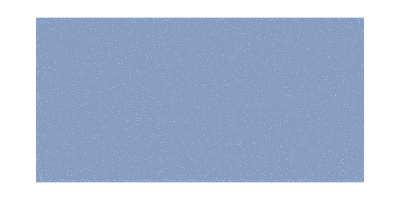

/home/san/Code/Laplace_eq/meshes/mesh.stl

```mathematica
model =DiscretizeRegion[ImplicitRegion[y>= 0 && y <= 2 && 0<=x<=4, {{x,0,4},{y,-1,2}}], MaxCellMeasure->0.001]
Export["/home/san/Code/Laplace_eq/meshes/mesh.stl", model,  {"STL", "BinaryFormat" -> False}]
```

```mathematica
op=-Laplacian[u[x,y],{x,y}];
```

```mathematica
gammaD={
DirichletCondition[u[x,y]==usol[x,y,250]//N,x==0&&0<=y<=2],
DirichletCondition[u[x,y]==usol[x,y,250]//N,x==4&&0<=y<=2],
DirichletCondition[u[x,y]==usol[x,y,250]//N,y==0&&0<=x<=4],
DirichletCondition[u[x,y]==usol[x,y,250]//N,y==2&&0<=x<=4]
};
```

```mathematica
ufun=NDSolveValue[{op==0,gammaD},u,{x,y}∈ImplicitRegion[y>= 0 && y <= 2 && 0<=x<=4, {{x,0,4},{y,0,2}}], Method->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->0.001,"MeshElementType"->TriangleElement}}]
```

InterpolatingFunction[{{0., 4.}, {0., 2.}}, <>]

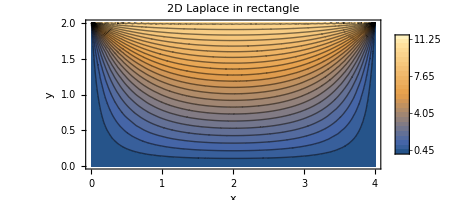

```mathematica
ContourPlot[ufun[x,y],{x,y}∈ImplicitRegion[y>= 0 && y <= 2 && 0<=x<=4, {{x,0,4},{y,-1,2}}],AspectRatio->Automatic,FrameLabel->{"x","y"},PlotLabel->"2D Laplace in rectangle",PlotLegends->Automatic, Contours->25]
```

```mathematica
usol[3.976470588235294,1.976744186046512,250] - ufun[3.976470588235294,1.976744186046512]
```

-0.158053

```mathematica
Err = {};
For[k = 1, k < Length@Z, ++k,AppendTo[Err,Abs[ ufun[X[[k]],Y[[k]]]-usol[X[[k]],Y[[k]],250 ]]]]
```

```mathematica
Max[Err]
```

0.158053